```mathematica
Needs["NumericalCalculus`"];
Needs["ColorBar`"];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
Ic1=Quantity[5*10^-6,"Ampere"];
EJ=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EL=3EJ
(*EJ2=α EJ1*)
(*EL=β EJ1*)
```

2618.942

7856.826

## 2 JJs/Arm

### Precompute joint element

```mathematica
precomputeElement2[EJ_]:=Module[{t1,ϕ,ϕm1,int1,fm,res,sres},
t1=Monitor[Table[
res=Table[
(fm=FindMinimum[-EJ (Cos[ϕm1]+ Cos[ϕ-ϕm1]-2), {ϕm1, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1-2π,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]]+π,2π]-π}
,{ϕ,-2π,2.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase1

```mathematica
h2=Quiet[precomputeElement2[EJ]];
```

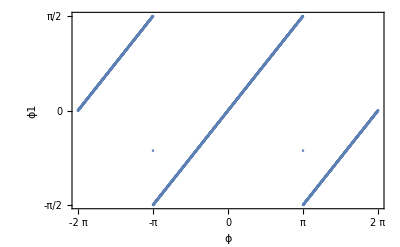

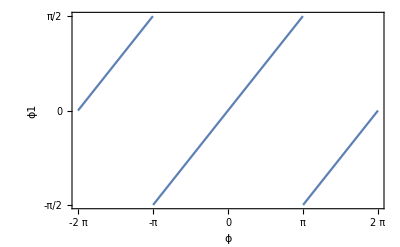

```mathematica
midphase1=Table[{h2[[i,1]],h2[[i,3]]},{i,1,Length[h2]}];
ListPlot[midphase1,Frame->True, FrameLabel->{"ϕ","ϕ1"}, FrameTicks->{{π Range[-1,1,1/4],None},{π Range[-2,2,1/4],None}}]
Plot[1/2(Mod[x+π,2π]-π),{x,-2π,2π},Frame->True, FrameLabel->{"ϕ","ϕ1"}, FrameTicks->{{π Range[-1,1,1/4],None},{π Range[-2,2,1/4],None}}]
```

### Hamiltonian(2 JJs)

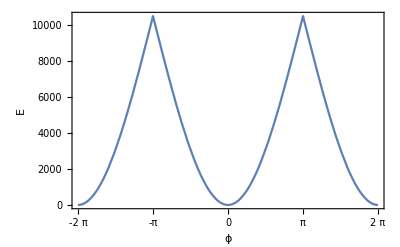

```mathematica
hm2=Interpolation[Table[{h2[[i,1]],2*h2[[i,2]]},{i,1,Length[h2]}]];
Plot[hm2[x],{x,-2π,2π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[-2,2,1/4],None}}]
```

## 3 JJs/Arm

### Precompute joint element

```mathematica
fϕm1[ϕm2_]:=1/2(Mod[ϕm2+π,2π]-π);
precomputeElement3[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,int1,fm,res,sres},
t1=Monitor[Table[
res=Table[
ϕm1=fϕm1[ϕm2];
(fm=FindMinimum[-EJ (Cos[ϕm1]+Cos[ϕm2-ϕm1]+Cos[ϕ-ϕm2]-3), {ϕm2, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]]+π,2π]-π}
,{ϕ,-2π,2.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase2

```mathematica
h3=Quiet[precomputeElement3[EJ]];
```

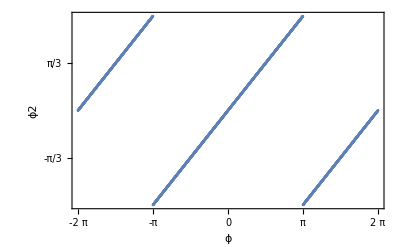

```mathematica
midphase2=Table[{h3[[i,1]],h3[[i,3]]},{i,1,Length[h3]}];
ListPlot[midphase2,Frame->True, FrameLabel->{"ϕ","ϕ2"}, FrameTicks->{{π Range[-1,1,1/3],None},{π Range[-2,2,1/4],None}}]
```

### Hamiltonian(3 JJs)

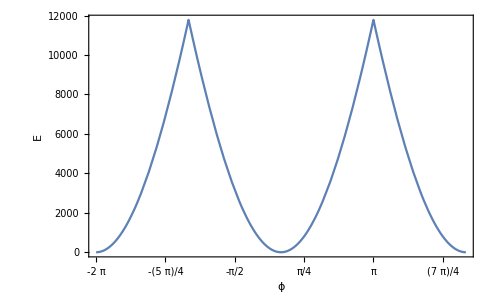

```mathematica
hm3=Interpolation[Table[{h3[[i,1]],3*h3[[i,2]]},{i,1,Length[h3]}]];
Plot[hm3[x],{x,-2π,2π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[-2,2,1/4],None}}]
```

## 4 JJs/Arm

### Precompute joint element

```mathematica
fϕm2[ϕm3_]:=2/3(Mod[ϕm3-π,2π]-π);
precomputeElement4[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,ϕm3,int1,fm,res,sres},
t1=Monitor[Table[
res=Table[
ϕm2=fϕm2[ϕm3];
ϕm1=fϕm1[ϕm2];
(fm=FindMinimum[-EJ( Cos[ϕm1]+ Cos[ϕm2-ϕm1]+Cos[ϕm3-ϕm2]+ Cos[ϕ-ϕm3]-4), {ϕm3, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]]-π,2π]-π}
,{ϕ,-π,1.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase3

```mathematica
h4=Quiet[precomputeElement4[EJ]];
```

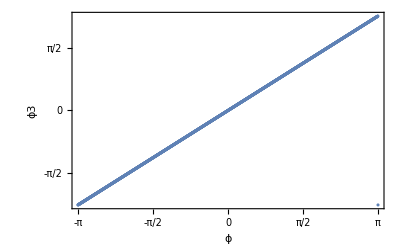

```mathematica
midphase3=Table[{h4[[i,1]],h4[[i,3]]},{i,1,Length[h4]}];
ListPlot[midphase3,Frame->True, FrameLabel->{"ϕ","ϕ3"}, FrameTicks->{{π Range[-1,1,1/4],None},{π Range[-1,1,1/4],None}}]
```

### Hamiltonian(4 JJs)

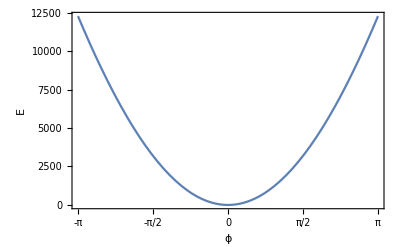

```mathematica
hm4=Interpolation[Table[{h4[[i,1]],4*h4[[i,2]]},{i,1,Length[h4]}]];
Plot[hm4[x],{x,-π,π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[-1,1,1/4],None}}]
```

## 5 JJs/Arm

### Precompute joint element

```mathematica
fϕm3[ϕm4_]:=3/4(Mod[ϕm4-π,2π]-π);
precomputeElement5[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,ϕm3,ϕm4,int1,fm,res,sres},
t1=Monitor[Table[
res=Table[
ϕm3=fϕm3[ϕm4];
ϕm2=fϕm2[ϕm3];
ϕm1=fϕm1[ϕm2];
(fm=FindMinimum[-EJ (Cos[ϕm1]+Cos[ϕm2-ϕm1]+ Cos[ϕm3-ϕm2]+ Cos[ϕm4-ϕm3]+Cos[ϕ-ϕm4]-5), {ϕm4, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]]-π,2π]-π}
,{ϕ,-π,1.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase4

```mathematica
h5=Quiet[precomputeElement5[EJ]];
```

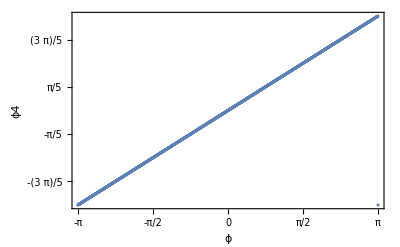

```mathematica
midphase4=Table[{h5[[i,1]],h5[[i,3]]},{i,1,Length[h5]}];
ListPlot[midphase4,Frame->True, FrameLabel->{"ϕ","ϕ4"}, FrameTicks->{{π Range[-1,1,1/5],None},{π Range[-1,1,1/4],None}}]
```

### Hamiltonian(5 JJs)

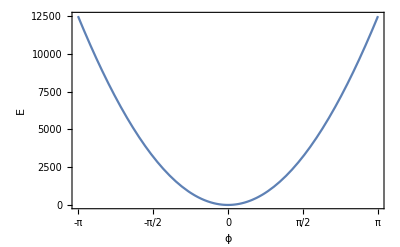

```mathematica
hm5=Interpolation[Table[{h5[[i,1]],5*h5[[i,2]]},{i,1,Length[h5]}]];
Plot[hm5[x],{x,-π,π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[-1,1,1/4],None}}]
```

## Altogether

### get energy functions

```mathematica
getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+π,2π]-π]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

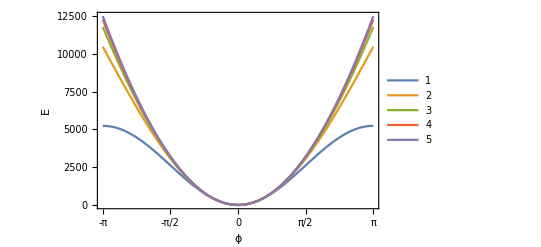

```mathematica
hm1[x_]:=-EJ (Cos[x]-1);
hmlist={hm1,hm2,hm3,hm4,hm5};
Plot[Evaluate[Table[hmlist[[i]][x],{i,1,Length[hmlist]}]],{x,-π,π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[-1,1,1/4],None}},PlotLegends->{"1","2","3","4","5"}]
```

## Total Hamiltonian

```mathematica
Clear[H]
H[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕext_,Harm_,EL_]:=
(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
Hn[ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ,ϕ4_?NumericQ,ϕ5_?NumericQ,ϕext_?NumericQ,Harm_,EL_?NumericQ]:=(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
```

### Find minimum energy of the whole thing

```mathematica
ip=Table[RandomReal[{0,2π},4],50];
Monitor[For[listEmin={};j=1,j≤Length[hmlist],j++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕ1,ϕ2,ϕ3,ϕ4,0,ϕext,hmlist[[j]],EL],{ϕ1,ip[[i,1]]},{ϕ2,ip[[i,2]]},{ϕ3,ip[[i,3]]},{ϕ4,ip[[i,4]]}]];
{res[[1]],ϕ1,ϕ2,ϕ3,ϕ4}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/10}]
,ϕext];
listEmin=Insert[listEmin,t1,j]
],
j]
```

```mathematica
Export["Emin w dif JJ#(β=3).txt",listEmin];
```

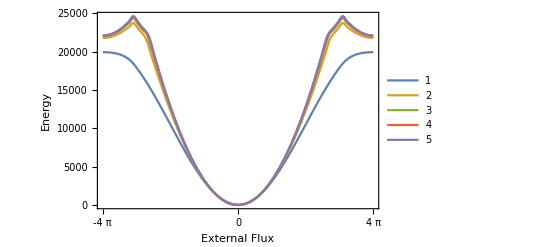

```mathematica
Plot[
Evaluate[Table[Interpolation[listEmin[[i,All,1,{1,2}]],Method->"Spline"][x],{i,1,Length[hmlist]}]],{x,-4π,4π},
 Frame->True, FrameLabel->{"External Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLegends->{"1","2","3","4","5"}
]
```

## Check Assumption

```mathematica
listEmin;
ϕnode[n_,i_]:=listEmin[[n,All,1,{1,2+i}]]
iptϕnode[n_,i_]:=Interpolation[ϕnode[n,i]]

ϕarm[n_,i_]:=Table[{listEmin[[n,j,1,1]],listEmin[[n,j,1,3+Mod[i,4]]]-listEmin[[n,j,1,2+i]]}
,{j,1,Length[listEmin[[n]]]}]
itpϕarm[n_,i_]:=Interpolation[ϕarm[n,i]]
```

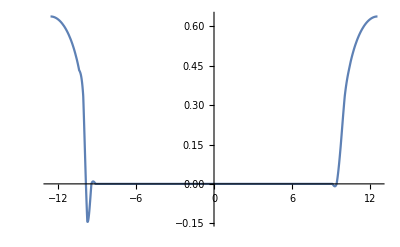

```mathematica
Plot[fϕm1[itpϕarm[1,1][x]],{x,-4π,4π},PlotRange->All]



(*Plot[itpϕnode[4,1][x],{x,-4π,4π}]
Plot[itpϕnode[4,2][x],{x,-4π,4π}]
Plot[itpϕnode[4,3][x],{x,-4π,4π},PlotRange->All]
Plot[itpϕnode[4,4][x],{x,-4π,4π}]*)
```

## Find Derivatives

```mathematica
Monitor[
For[listd={};j=1,j<=Length[listEmin],j++,
Monitor[
t2=Table[
{ϕext,ϕ1,ϕ2,ϕ3,ϕ4}=listEmin[[j,i,1,{1,3,4,5,6}]];
ϕf=0;

h00=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ1,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ2,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ3,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ4,-a ϕw+ϕf, ϕext,hmlist[[j]],EJ];
{ϕext,
(ND[h00/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[ND[ND[h00/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,1},0]),
(*xyzvalue,*)
(ND[ND[h00/.{a->1,ϕy->0,ϕw->0},{ϕx,2},0],{ϕz,2},0])/4,
(ND[h00/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24,
(ND[ND[ND[h00/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,3},0])/6
}
,{i,Length[listEmin[[j]]]}]
,listEmin[[j,i,1,1]]];
listd=Insert[listd,t2,j]]
,j]
```

```mathematica
Export["Derivatives w dif JJ#(β=3).txt",listd];
```

```mathematica
x2=Table[Interpolation[listd[[i,All,{1,2}]]],{i,1,Length[hmlist]}];
xyz=Table[Interpolation[listd[[i,All,{1,3}]]],{i,1,Length[hmlist]}];x2z2=Table[Interpolation[listd[[i,All,{1,4}]]],{i,1,Length[hmlist]}];x4=Table[Interpolation[listd[[i,All,{1,5}]]],{i,1,Length[hmlist]}];
xyz3=Table[Interpolation[listd[[i,All,{1,6}]]],{i,1,Length[hmlist]}];
```

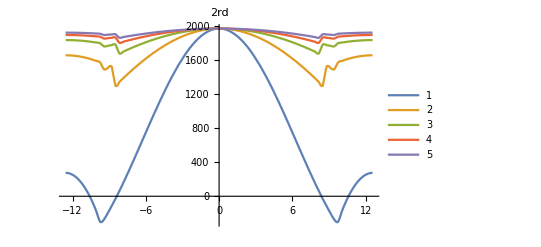

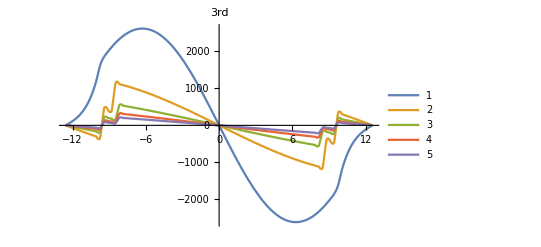

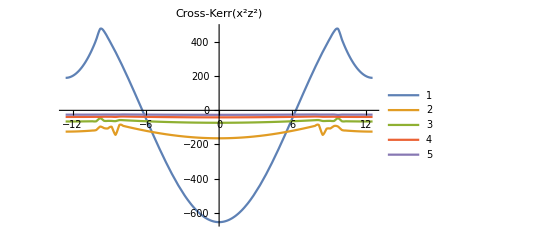

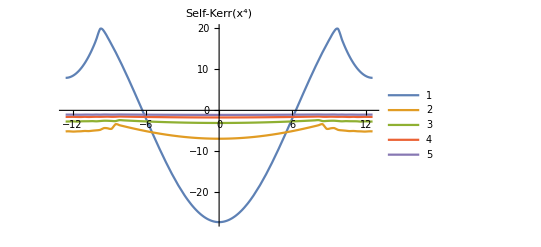

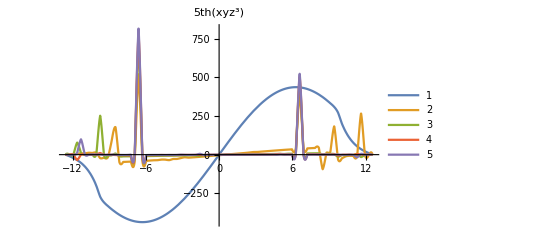

```mathematica
Plot[Evaluate[Table[x2[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"2rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[xyz[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x2z2[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr(x^2z^2)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x4[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr(x^4)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[xyz3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"5th(xyz^3)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
```

### Comparison of Kerr, 5th and 3rd

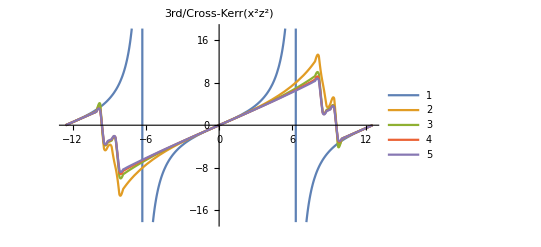

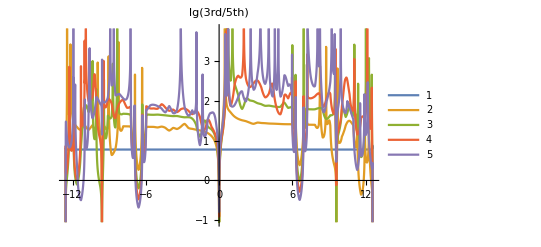

```mathematica
Plot[Evaluate[Table[xyz[[i]][x]/x2z2[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"3rd/Cross-Kerr(x^2z^2)",PlotLegends->{"1","2","3","4","5"}]
Plot[Evaluate[Table[Log10[Abs[xyz[[i]][x]/xyz3[[i]][x]]],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"lg(3rd/5th)",PlotLegends->{"1","2","3","4","5"}]
```

## Normalize 3rd

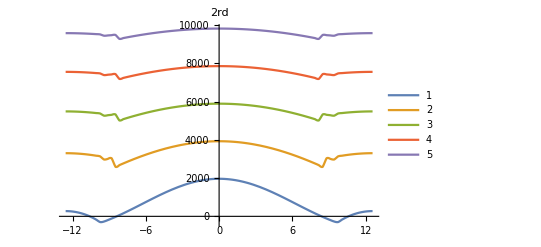

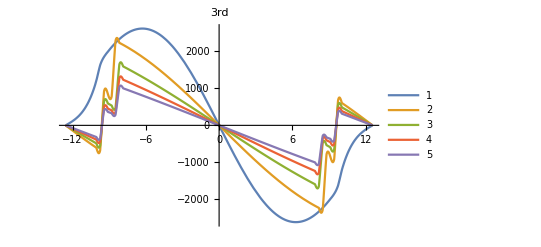

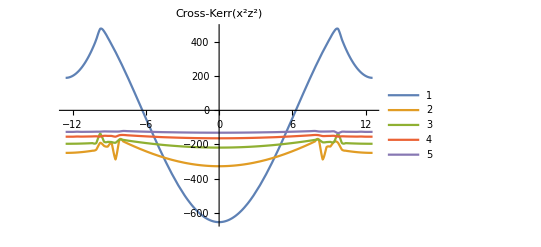

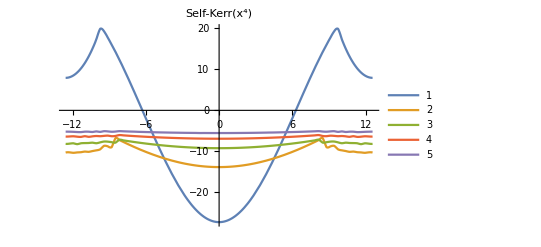

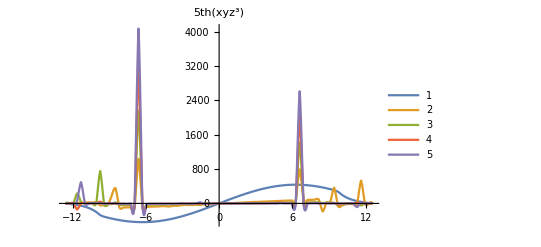

```mathematica
listdN3=ReplacePart[listd,{n_,ϕ_,k_}:>If[k>1,n listd[[n,ϕ,k]], listd[[n,ϕ,k]]]];
x2N3=Table[Interpolation[listdN3[[i,All,{1,2}]]],{i,1,Length[hmlist]}];
xyzN3=Table[Interpolation[listdN3[[i,All,{1,3}]]],{i,1,Length[hmlist]}];x2z2N3=Table[Interpolation[listdN3[[i,All,{1,4}]]],{i,1,Length[hmlist]}];x4N3=Table[Interpolation[listdN3[[i,All,{1,5}]]],{i,1,Length[hmlist]}];
xyz3N3=Table[Interpolation[listdN3[[i,All,{1,6}]]],{i,1,Length[hmlist]}];

Plot[Evaluate[Table[x2N3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"2rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[xyzN3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x2z2N3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr(x^2z^2)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x4N3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr(x^4)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[xyz3N3[[i]][x],{i,1,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"5th(xyz^3)",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
```